## ^163Lu - March 2020 Energies

### Fitting the experimental energies

```mathematica
TSD1={{8.5,0.1966},{10.5,0.4597},{12.5,0.7746},{14.5,1.1609},{16.5,1.6112},{18.5,2.1265},{20.5,2.7051},{22.5,3.3441},{24.5,4.0411},{26.5,4.7937},{28.5,5.5992},{30.5,6.457},{32.5,7.3667},{34.5,8.3293},{36.5,9.3458},{38.5,10.4169},{40.5,11.5431},{42.5,12.7224},{44.5,13.9491},{46.5,15.2181},{48.5,16.5221}};
TSD2={{13.5,1.3394},{15.5,1.7467},{17.5,2.2184},{19.5,2.7527},{21.5,3.3484},{23.5,4.003},{25.5,4.7143},{27.5,5.4805},{29.5,6.3004},{31.5,7.1733},{33.5,8.0998},{35.5,9.08},{37.5,10.1147},{39.5,11.2036},{41.5,12.3466},{43.5,13.5441},{45.5,14.7911}};
TSD3={{16.5,2.1237},{18.5,2.6293},{20.5,3.1973},{22.5,3.8243},{24.5,4.5094},{26.5,5.2506},{28.5,6.0465},{30.5,6.8963},{32.5,7.7988},{34.5,8.7546},{36.5,9.7638},{38.5,10.8268},{40.5,11.9392},{42.5,13.0861}};
TSD4={{23.5,4.58},{25.5,5.2251},{27.5,5.9273},{29.5,6.6819},{31.5,7.4919},{33.5,8.3573},{35.5,9.2778},{37.5,10.2535},{39.5,11.2851},{41.5,12.3701}};
```

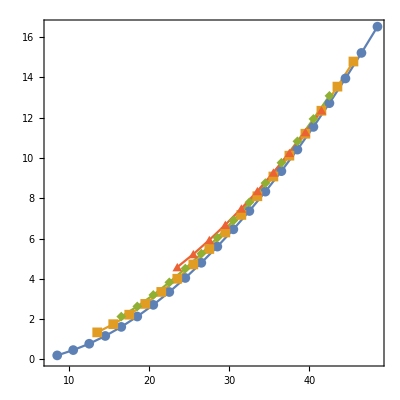

```mathematica
ListPlot[{TSD1,TSD2,TSD3,TSD4},Frame->True,Axes->False,Joined->True,AspectRatio->1,PlotMarkers->{Automatic, Medium}]
```

```mathematica
allbands={{8.5,0.1966},{10.5,0.4597},{12.5,0.7746},{14.5,1.1609},{16.5,1.6112},{18.5,2.1265},{20.5,2.7 051},{22.5,3.3441},{24.5,4.0411},{26.5,4.7937},{28.5,5.5992},{30.5,6.457},{32.5,7.3667},{34.5,8.3293},{36.5,9.3458},{38.5,10.4169},{40.5,11.5431},{42.5,12.7224},{44.5,13.9491},{46.5,15.2181},{48.5,16.5221},{13.5,1.3394},{15.5,1.7467},{17.5,2.2184},{19.5,2.7527},{21.5,3.3484},{23.5,4.003},{25.5,4.7143},{27.5,5.4805},{29.5,6.3004},{31.5,7.1733},{33.5,8.0998},{35.5,9.08},{37.5,10.1147},{39.5,11.2036},{41.5,12.34 66},{43.5,13.5441},{45.5,14.7911},{16.5,2.1237},{18.5,2.6293},{20.5,3.1973},{22.5,3.8243},{24.5,4.5094},{26.5,5.2506},{28.5,6.0465},{30.5,6.8963},{32.5,7.7988},{34.5,8.7546},{36.5,9.7638},{38.5,10.8268},{40.5,11.9392},{42.5,13.0861},{23.5,4.58},{25.5,5.2251},{27.5,5.9273},{29.5,6.6819},{31.5,7.4919},{33.5,8.3573},{35.5,9.2778},{37.5,10.2535},{39.5,11.2851},{41.5,12.3701}};
```

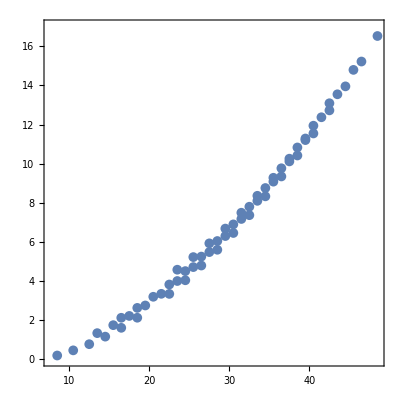

```mathematica
ListPlot[allbands,Frame->True,Axes->False,AspectRatio->1,Joined->False,PlotRange->{0,17},PlotMarkers->{Automatic, Medium}]
```

```mathematica
N[π,15]
```

3.14159265358979

## Formulas

```mathematica
moi[k_,i0_,γ_,β_]:=i0/(1+(5/(16π))^(1/2)*β)*(1-(5/(4π))^(1/2)β*Cos[γ*π/180+2/3 π*k]);
a1[i0_,γ_,β_]:=1/(2*moi[1,i0,γ,β]);
a2[i0_,γ_,β_]:=1/(2*moi[2,i0,γ,β]);
a3[i0_,γ_,β_]:=1/(2*moi[3,i0,γ,β]);
```

```mathematica
a1[50,19,0.38]
```

0.00948299

```mathematica
a2[50,19,0.38]
```

0.0107087

```mathematica
a3[50,19,0.38]
```

0.0144803

```mathematica
hMin[spin_,oddSpin_,i0_,v_,γ_,β_]:=(a2[i0,γ,β]+a3[i0,γ,β])*(spin+oddSpin)/2+a1[i0,γ,β]*(spin-oddSpin)^2-v*(2oddSpin-1)/(oddSpin+1)*Sin[γ*π/180+π/6];
b1[spin_,oddSpin_,i0_,v_,γ_,β_]:=-1*(((2spin-1)(a3[i0,γ,β]-a1[i0,γ,β])+2oddSpin*a1[i0,γ,β])((2spin-1)(a2[i0,γ,β]-a1[i0,γ,β])+2*oddSpin*a1[i0,γ,β])+8spin*oddSpin*a2[i0,γ,β]*a3[i0,γ,β]+((2oddSpin-1)*(a3[i0,γ,β]-a1[i0,γ,β])+2spin*a1[i0,γ,β]+v*(2oddSpin-1)/(oddSpin(oddSpin+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))*((2oddSpin-1)*(a2[i0,γ,β]-a1[i0,γ,β])+2spin*a1[i0,γ,β]+v*(2oddSpin-1)/(oddSpin(oddSpin+1))2 √3 Sin[γ*π/180]));
c1[spin_,oddSpin_,i0_,v_,γ_,β_]:=(((2spin-1)*(a3[i0,γ,β]-a1[i0,γ,β])+2oddSpin*a1[i0,γ,β])*((2oddSpin-1)*(a3[i0,γ,β]-a1[i0,γ,β])+2spin*a1[i0,γ,β]+v*(2oddSpin-1)/(oddSpin(oddSpin+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))-4spin*oddSpin*a3[i0,γ,β]^2)*(((2spin-1)*(a2[i0,γ,β]-a1[i0,γ,β])+2oddSpin*a1[i0,γ,β])*((2oddSpin-1)(a2[i0,γ,β]-a1[i0,γ,β])+2*spin*a1[i0,γ,β]+v*(2oddSpin-1)/(oddSpin*(oddSpin+1))2 √3 Sin[γ*π/180])-4spin*oddSpin*a2[i0,γ,β]^2);
Omega1[spin_,oddSpin_,i0_,v_,γ_,β_]:=√(1/2(-b1[spin,oddSpin,i0,v,γ,β]-(b1[spin,oddSpin,i0,v,γ,β]^2-4c1[spin,oddSpin,i0,v,γ,β])^(1/2)));
Omega2[spin_,oddSpin_,i0_,v_,γ_,β_]:=√(1/2(-b1[spin,oddSpin,i0,v,γ,β]+(b1[spin,oddSpin,i0,v,γ,β]^2-4c1[spin,oddSpin,i0,v,γ,β])^(1/2)));
```

```mathematica
energyExpression[n1_,n2_,spin_,oddSpin_,i0_,v_,γ_,β_]:=hMin[spin,oddSpin,i0,v,γ,β]+Omega1[spin,oddSpin,i0,v,γ,β]*(n1+1/2)+Omega2[spin,oddSpin,i0,v,γ,β]*(n2+1/2);
e0[i0_,v_,γ_,β_]:=energyExpression[0,0,6.5,6.5,i0,v,γ,b];
energyTSD1[spin_,i0_,v_,γ_,β_]:=energyExpression[0,0,spin,6.5,i0,v,γ,β]-e0[i0,v,γ,β];
energyTSD2[spin_,i0_,v_,γ_,β_]:=energyExpression[1,0,spin-1,6.5,i0,v,γ,β]-e0[i0,v,γ,β];
energyTSD3[spin_,i0_,v_,γ_,β_]:=energyExpression[2,0,spin-2,6.5,i0,v,γ,β]-e0[i0,v,γ,β];
energyTSD4[spin_,i0_,v_,γ_,β_]:=energyExpression[3,0,spin-3,4.5,i0,v,γ,β]-e0[i0,v,γ,β];
```

```mathematica
Do[Print[i," ",energyTSD1[i,99,0.5,19,0.38]," ",energyTSD2[i,99,0.5,19,0.38]," ",energyTSD3[i,99,0.5,19,0.38], " ",energyTSD4[i,99,0.5,19,0.38]],{i,0.5,52.5,2}]
```

0.5 0.378916-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.489589-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.615673-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.588523-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

2.5 0.309772-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.397575-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.498218-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.5042-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

4.5 0.278642-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.345256-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.423221-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.458374-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

6.5 0.285594-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.332096-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.388961-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.451172-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

8.5 0.330676-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.357831-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.394632-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.48267-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

10.5 0.413926-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.422313-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.439794-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.552906-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

12.5 0.535374-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.525452-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.524183-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.661895-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

14.5 0.69504-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.667191-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.647625-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.809636-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

16.5 0.892944-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.847486-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.810001-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 0.996115-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

18.5 1.1291-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 1.06631-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 1.01122-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 1.22131-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

20.5 1.40351-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 1.32363-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 1.25121-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 1.4852-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

22.5 1.71619-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 1.61943-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 1.52992-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 1.78776-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

24.5 2.06715-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 1.95369-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 1.84731-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 2.12895-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

26.5 2.45638-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 2.32639-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 2.20332-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 2.50877-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

28.5 2.88391-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 2.73754-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 2.59794-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 2.92717-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

30.5 3.34972-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 3.1871-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 3.03113-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 3.38415-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

32.5 3.85382-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 3.67508-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 3.50287-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 3.87967-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

34.5 4.39621-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 4.20146-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 4.01313-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 4.41373-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

36.5 4.9769-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 4.76624-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 4.5619-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 4.9863-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

38.5 5.59589-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 5.36941-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 5.14916-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 5.59737-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

40.5 6.25317-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 6.01096-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 5.77489-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 6.24692-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

42.5 6.94876-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 6.69089-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 6.43909-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 6.93494-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

44.5 7.68265-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 7.4092-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 7.14173-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 7.66142-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

46.5 8.45484-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 8.16587-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 7.88282-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 8.42636-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

48.5 9.26534-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 8.9609-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 8.66234-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 9.22973-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

50.5 10.1141-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 9.7943-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 9.48028-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 10.0715-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))

52.5 11.0012-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 10.6661-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 10.3366-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))))) 10.9518-6.5 ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))-1/(2 √2)(√((0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))+√((-(0.00862157 (1+1/4 b √(5/π))^2)/((1-1/2 b √(5/π) Cos[(19 π)/180]) (1+1/2 b √(5/π) Sin[(11 π)/180]))-((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) ((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))-(0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))))^2-4 (-(0.00431078 (1+1/4 b √(5/π))^2)/(1-1/2 b √(5/π) Cos[(19 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180])))) (0.418518+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. ((1+1/4 b √(5/π))/(198 (1-1/2 b √(5/π) Cos[(19 π)/180]))-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))))) (-(0.00431078 (1+1/4 b √(5/π))^2)/(1+1/2 b √(5/π) Sin[(11 π)/180])^2+((0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180])))) (0.138806+(0.0656566 (1+1/4 b √(5/π)))/(1+1/2 b √(5/π) Cos[(41 π)/180])+12. (-(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Cos[(41 π)/180]))+(1+1/4 b √(5/π))/(198 (1+1/2 b √(5/π) Sin[(11 π)/180]))))))))